```mathematica
europes=CountryData["Europe"]
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

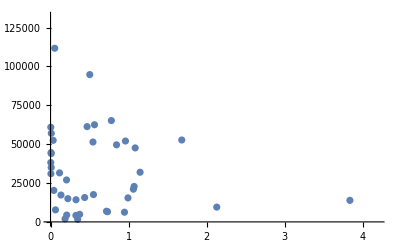

```mathematica
europesPopGDP = Map[Block[{tmp = #},Map[CountryData[tmp,#]&,{"Population","GDPPerCapita"}]]&,europes] ;
ListPlot[europesPopGDP]
```

```mathematica
Solve[(n (n-1))(x(x-1)),{x,n},{x,n}]
```

Solve::disj: Variable lists {x, n} and {x, n} should be disjoint.

```mathematica
Solve[((x-a)(x-a-1))/((x-1)x) == 1/2, {x,a}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→1/2 (-1+2 x-√(1-2 x+2 x^2))},{a→1/2 (-1+2 x+√(1-2 x+2 x^2))}}